# ECUACIONES DIFERENCIALES

## ECUACIONES DIFERENCIALES CON MATHEMATICA:

Fis. Jorge Chávez Carlos

Con mathematica es posible calcular la solución de ecuaciones diferenciales usando un comando muy sencillo de usar dado por:

DSolve[eqn,y,x]

resuelve una ecuación diferencial para una función y, con variable independiente x.

## Ejemplo 1:

```mathematica
DSolve[x y'[x] + 2y[x] == 4 x^2, y[x], x]
```

{{y[x]→x^2+C[1]/x^2}}

C[1] se refiere a Constante1

## Ejemplo 2:

```mathematica
DSolve[n'[x] ==0.2 n[x] , n[x], x]
```

{{n[x]→ⅇ^(0.2 x) C[1]}}

Si se tiene una condición inicial por ejemplo n(0) = 3

```mathematica
DSolve[{n'[x]==0.2n[x],n[0]==3},n[x],x]
```

{{n[x]→3. ⅇ^(0.2 x)}}

Si uno quiere graficar la solución particular se escribe :

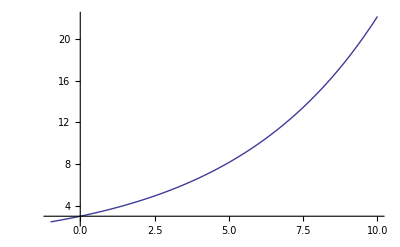

```mathematica
Plot[n[x]/.%,{x,-1,10}]
```

## Ejemplo 3:

```mathematica
DSolve[y'[x] +x y[x] ==3 , y[x], x]
```

{{y[x]→ⅇ^(-x^2/2) C[1]+3 ⅇ^(-x^2/2) √(π/2) Erfi[x/(√2)]}}